```mathematica
(*Statistical analysis of frequency shifts calculated by SolEFP*)
(*This Mathematica notebook processes SolEFP output .dat files*)
(*The output mean frequency is required as an input to lineshape conversion*)

(*Set directory*)
SetDirectory["/Users/Sherina/Desktop"];

(*SolEFP data*)
SolEFPFreq=Import["1cll-l105c-125.0ns-20ns-stat-additive-processed.dat","Table"][[2;;,;;]];
```

```mathematica
(*Coulomb*)
(*Data*)
Cou=SolEFPFreq[[;;,3;;6]];
Env=SolEFPFreq[[;;,19]];
```

```mathematica
(*Total Coulomb shift*)
CouTot=Table[Sum[Cou[[i,j]],{j,1,4}]+Env[[i]],{i,1,Length[Cou]}];
(*Averages*)
CouAve=Mean[CouTot];
(*Standard deviations*)
CouStd=StandardDeviation[CouTot];
```

```mathematica
(*Polarization*)
(*Data*)
Pol=SolEFPFreq[[;;,7;;8]];
```

```mathematica
(*Total polarization shift*)
PolTot=Table[Sum[Pol[[i,j]],{j,1,2}],{i,1,Length[Pol]}];
(*Averages*)
PolAve=Mean[PolTot];
(*Standard deviations*)
PolStd=StandardDeviation[PolTot];
```

```mathematica
(*Repulsion*)
(*Data*)
Rep=SolEFPFreq[[;;,9;;10]];
```

```mathematica
(*Total repulsion shift*)
RepTot=Table[Sum[Rep[[i,j]],{j,1,2}],{i,1,Length[Rep]}];
(*Averages*)
RepAve=Mean[RepTot];
(*Standard deviations*)
RepStd=StandardDeviation[RepTot];
```

```mathematica
(*Dispersion*)
(*Data*)
Dis=SolEFPFreq[[;;,11;;12]];
```

```mathematica
(*Total dispersion shift*)
DisTot=Table[Sum[Dis[[i,j]],{j,1,2}],{i,1,Length[Dis]}];
(*Averages*)
DisAve=Mean[DisTot];
(*Standard deviations*)
DisStd=StandardDeviation[DisTot];
```

```mathematica
(*Total frequency shift*)
(*dw=dw(SolCAMM-CONH)+dw(SolEFP)+dw(through-bond)(+dw(error))*)
thruBond=-3.1(*cm^-1*);

(*Data*)
TTot=SolEFPFreq[[;;,20]]+ thruBond;
(*Averages*)
TTotAve=Mean[TTot];
(*Standard deviations*)
TTotStd=StandardDeviation[TTot];
```

```mathematica
(*Convert to frequencies*)
(*freq_calc = freq_MeSCN_gasphase_experiment+TTot*)
MeSCNGasFreq=2171(*cm^-1*);
(*Data*)
Freq=TTot+MeSCNGasFreq;
(*Averages*)
FreqAve=Mean[Freq];
(*Standard deviations*)
FreqStd=StandardDeviation[Freq];
```

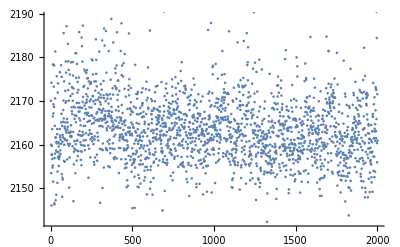

```mathematica
(*Freq trj*)
ListPlot[Freq]
```

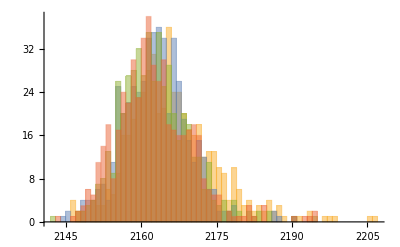

```mathematica
(*interval histograms*)
Histogram[{Freq[[1;;500]],Freq[[500;;1000]],Freq[[1000;;1500]],Freq[[1500;;2000]]},50]
```

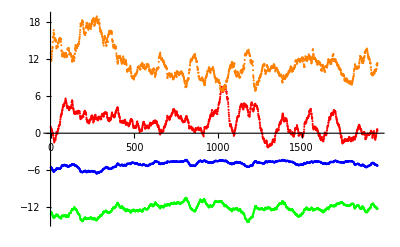

```mathematica
(*SolEFP component trj*)
ListPlot[{MovingAverage[CouTot,50],MovingAverage[PolTot,50],MovingAverage[RepTot,50],MovingAverage[DisTot,50]},PlotRange->{All,All},PlotStyle->{Red,Blue,Orange,Green}]
```

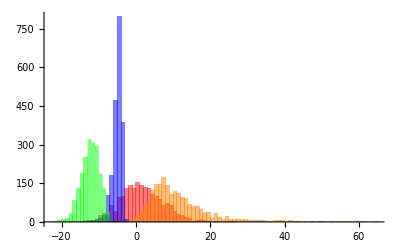

```mathematica
(*Histograms*)
Histogram[{CouTot,PolTot,RepTot,DisTot},100,ChartStyle->{Red,Blue,Orange,Green}]
```

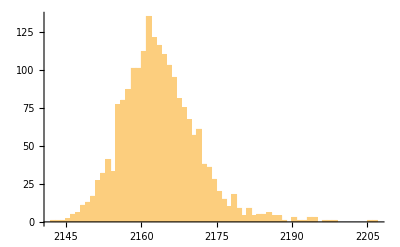

```mathematica
Histogram[Freq,50]
```

```mathematica
(*Tables*)
(*NMF=N-methylformamide; AcA=acetamide; NMA=N-methylacetamide*)
TableForm[{{CouAve,PolAve,RepAve,DisAve,TTotAve,FreqAve},{CouStd,PolStd,RepStd,DisStd,TTotStd,FreqStd}},TableHeadings->{{"Ave","Std"},{"Cou cm^-1","Pol cm^-1","Rep cm^-1","Dis cm^-1","TTot cm^-1","Freq cm^-1"}}]
```

| Cou cm^-1 | Pol cm^-1 | Rep cm^-1 | Dis cm^-1 | TTot cm^-1 | Freq cm^-1
Ave | 1.69763 | -5.01436 | 11.3864 | -12.2788 | -7.30918 | 2163.69
Std | 5.80396 | 1.30162 | 8.43553 | 2.46822 | 7.63605 | 7.63605

```mathematica
l105n1=Freq;
```

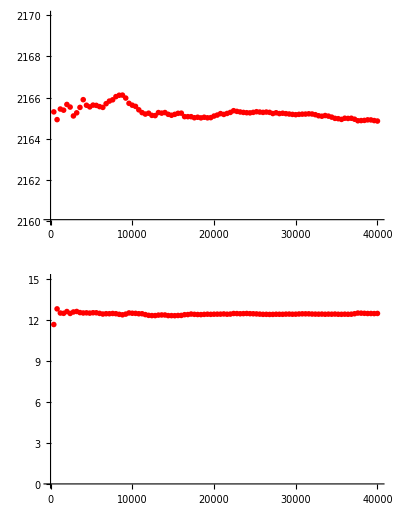

```mathematica
npart=100;
part=IntegerPart[Length[Freq]/npart];
GraphicsColumn[{ListPlot[Table[{part*i,Mean[Freq[[;;part*i]]]},{i,1,npart}],PlotRange->{2160,2170},PlotStyle->{PointSize[0.01],Red}],ListPlot[Table[{part*i,StandardDeviation[Freq[[;;part*i]]]},{i,1,npart}],PlotRange->{0,15},PlotStyle->{PointSize[0.01],Red}]}]
```